```mathematica
Exit[];
```

```mathematica
$Assumptions=  r>0 && Element[m,Integers] && Element[n,Integers]  && s>0
```

r>0&&m∈Integers&&n∈Integers&&s>0

# 2-d Dirac

```mathematica
f1[r_,En_]:={{(m-1)/r,I*(En-r^p)},{I*(En-r^p),-m/r}};f1[r,En]//MatrixForm
```

((-1+m)/r | ⅈ (En-r^p)
ⅈ (En-r^p) | -m/r)

# Diagonaldarstellung für r gegen Infinity

```mathematica
V={{1,1},{-1,1}};Simplify[V.f1[r,En].Inverse[V]]//MatrixForm
```

(ⅈ En-1/(2 r)-ⅈ r^p | (1-2 m)/(2 r)
(1-2 m)/(2 r) | -ⅈ En-1/(2 r)+ⅈ r^p)

```mathematica
Inverse[V].{0,C}
```

{-C/2,C/2}

# Potenzreihenansatz mit richtigem Rangverhalten

# m>=1

```mathematica
s=m-1;p=2;
```

```mathematica
f1[r,En]//MatrixForm
```

((-1+m)/r | ⅈ (En-r^2)
ⅈ (En-r^2) | -m/r)

```mathematica
u={F[x],G[x]}*x^(s)
```

{x^(-1+m) F[x],x^(-1+m) G[x]}

```mathematica
r[x_]:=x;
```

```mathematica
g1=Collect[Expand[Simplify[Expand[-(D[u,x]-r'[x]*f1[r[x],En].u)/x^(s-0)]]],{x^n,a[n],b[n],F[x],G[x]}];
g1
```

{(ⅈ En-ⅈ x^2) G[x]-F'[x],(ⅈ En-ⅈ x^2) F[x]+(1/x-(2 m)/x) G[x]-G'[x]}

```mathematica
m=2;
```

```mathematica
f2[x_,En_]:={{0,(ⅈ En-ⅈ x^p) },{(ⅈ En-ⅈ x^p),(1/x-(2 m)/x) }};f2[r,En]//MatrixForm
```

(0 | (-0.286517+5.53302 ⅈ)-ⅈ r^2
(-0.286517+5.53302 ⅈ)-ⅈ r^2 | -3/r)

```mathematica
u={F[x],G[x]}*Exp[I*x^(p+1)/(p+1)]
```

{ⅇ^((ⅈ x^3)/3) F[x],ⅇ^((ⅈ x^3)/3) G[x]}

```mathematica
g1=Collect[Expand[Simplify[Expand[-(D[u,x]-r'[x]*f2[r[x],En].u)/Exp[I*x^(p+1)/(p+1)]]]],{x^n,a[n],b[n],F[x],G[x]}];
g1
```

{-ⅈ x^2 F[x]+(ⅈ En-ⅈ x^2) G[x]-F'[x],(ⅈ En-ⅈ x^2) F[x]+(-3/x-ⅈ x^2) G[x]-G'[x]}

```mathematica
f[x_,En_]:={{-ⅈ x^p ,(ⅈ En-ⅈ x^p)},{(ⅈ En-ⅈ x^p) ,(1/x-(2 m)/x-ⅈ x^p) }};f[r,En]//MatrixForm
```

(-ⅈ r^2 | (-0.286517+5.53302 ⅈ)-ⅈ r^2
(-0.286517+5.53302 ⅈ)-ⅈ r^2 | -3/r-ⅈ r^2)

```mathematica
u={a[n],b[n]}*x^n
```

{x^n a[n],x^n b[n]}

```mathematica
p=2;
```

```mathematica
g1=Collect[Expand[Simplify[Expand[-(D[u,x]-r'[x]*f[r[x],En].u)*x]]],{x^n,a[n],b[n],F[x],G[x]}];
g1
```

{x^n ((-n-ⅈ x^3) a[n]+(ⅈ En x-ⅈ x^3) b[n]),x^n ((ⅈ En x-ⅈ x^3) a[n]+(1-2 m-n-ⅈ x^3) b[n])}

```mathematica
g2=Table[Simplify[Sum[D[g1,{x,n2}]/n2!,{n,0,10}]/.x->0],{n2,0,10}];g2//MatrixForm
```

(0 | (1-2 m) b[0]
-a[1]+ⅈ En b[0] | ⅈ En a[0]-2 m b[1]
-2 a[2]+ⅈ En b[1] | ⅈ En a[1]-(1+2 m) b[2]
-ⅈ (a[0]-3 ⅈ a[3]+b[0]-En b[2]) | -ⅈ (a[0]-En a[2]+b[0]-2 ⅈ b[3]-2 ⅈ m b[3])
-ⅈ (a[1]-4 ⅈ a[4]+b[1]-En b[3]) | -ⅈ (a[1]-En a[3]+b[1]-3 ⅈ b[4]-2 ⅈ m b[4])
-ⅈ (a[2]-5 ⅈ a[5]+b[2]-En b[4]) | -ⅈ (a[2]-En a[4]+b[2]-4 ⅈ b[5]-2 ⅈ m b[5])
-ⅈ (a[3]-6 ⅈ a[6]+b[3]-En b[5]) | -ⅈ (a[3]-En a[5]+b[3]-5 ⅈ b[6]-2 ⅈ m b[6])
-ⅈ (a[4]-7 ⅈ a[7]+b[4]-En b[6]) | -ⅈ (a[4]-En a[6]+b[4]-6 ⅈ b[7]-2 ⅈ m b[7])
-ⅈ (a[5]-8 ⅈ a[8]+b[5]-En b[7]) | -ⅈ (a[5]-En a[7]+b[5]-7 ⅈ b[8]-2 ⅈ m b[8])
-ⅈ (a[6]-9 ⅈ a[9]+b[6]-En b[8]) | -ⅈ (a[6]-En a[8]+b[6]-8 ⅈ b[9]-2 ⅈ m b[9])
-ⅈ (a[7]-10 ⅈ a[10]+b[7]-En b[9]) | -ⅈ (a[7]-En a[9]+b[7]-9 ⅈ b[10]-2 ⅈ m b[10]))

```mathematica
a[0]=1;b[0]=0; b[1]=ⅈ En a[0]/2/ m ;a[2]=ⅈ En b[1]/2 ;a[1]=0;b[2]=0;
```

```mathematica
a[1]=.;a[2]=.;b[1]=.;b[0]=.;a[0]=.;b[2]=.;a[n_]=.;b[n_]=.;
```

```mathematica
b[n_]:=I/(n-1+2 m)* ( En a[n-1]-a[n-3]-b[n-3]);a[n_]:=1/n ⅈ (-a[n-3]+En b[n-1]-b[n-3])
```

```mathematica
Un[Ene_,mm_,nN_,x_]:=Module[{n,U1,U2,U3,U4,Erg},
U1={a[0],b[0]};U2={a[1],b[1]};U3={a[2],b[2]};
Erg=U1+U2*x+U3*x^2;
For[n=3,n≤nN,n++,
U4=Simplify[{1/n ⅈ (Ene U3[[2]]-U1[[1]]-U1[[2]]),I/(n-1+2 mm)* (Ene U3[[1]]-U1[[1]]-U1[[2]])}]//N;
U1=U2;U2=U3;U3=U4;
Erg+=U3*x^n;

];

Erg]
```

# zur Probe

```mathematica
Uno[Ene_,m_,nN_,x_]:=Module[{n,U,Erg=0},
U={{a[0],b[0]}};
For[n=1,n≤nN+1,n++,
AppendTo[U,{a[n],b[n]}]
];
For[n=0,n≤nN,n++,
Erg+=U[[n+1]]*x^n;
];
Erg
]
```

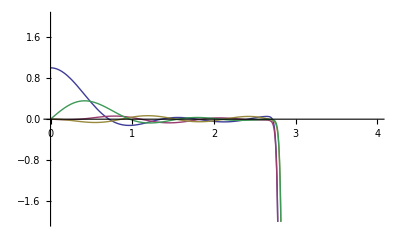

```mathematica
Ge={Re[#],Im[#]}&[Un[En,m,150,x]];Plot[Ge,{x,0,4},PlotRange->{-2,2}]
```

```mathematica
Analytische Lösung an stelle x mit güte g
```

```mathematica
U[Ene_,mm_,g_,x_]:=Module[{n=2,U1,U2,U3,U4,Erg},
U1={a[0],b[0]};U2={a[1],b[1]};U3={a[2],b[2]};
Erg=U1+U2*x+U3*x^2;
While[Sqrt[Abs[U3.Conjugate[U3]*x^(2n)]]>g,n++;
U4=Simplify[{1/n ⅈ (Ene U3[[2]]-U1[[1]]-U1[[2]]),I/(n-1+2 mm)* (Ene U3[[1]]-U1[[1]]-U1[[2]])}]//N;
U1=U2;U2=U3;U3=U4;
Erg+=U3*x^n;

];

{Erg,n}]
```

```mathematica
U[5.533021207627789+0.2865166733657229 ⅈ,2,10^-10,1]
```

{{-0.119165+0.0406181 ⅈ,0.030514-0.0178352 ⅈ},44}

# Berechnung der Eigenwerte

```mathematica
f3[rr_,Ennn_]=V.f[rr,Ennn].Inverse[V];f[erd,Ens]//MatrixForm
```

(-ⅈ erd^2 | ⅈ Ens-ⅈ erd^2
ⅈ Ens-ⅈ erd^2 | -3/erd-ⅈ erd^2)

55

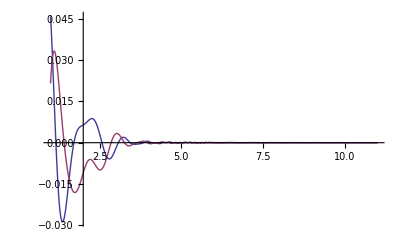

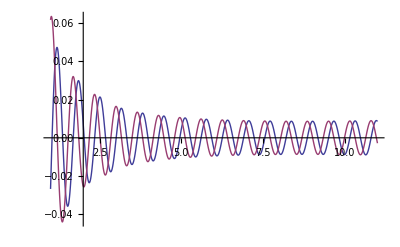

```mathematica
nn=5000;S=1;h=10/nn;ra=1;En=9.66789439439588+0.17121583336042184 ⅈ;m=2;r=1;
NN=U[En,m,10^-10,r];NN[[2]]
k=V.NN[[1]];
kK={{r,k}};
Do[
k0=h*f3[r,En].k;k1=h*f3[r+h/2,En].(k+k0/2);k2=h*f3[r+h/2,En].(k+k1/2);k3=h*f3[r+h,En].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);r+=h;
AppendTo[kK,{r,k}],{nn}];

ListPlot[Join[{ {#[[1]],Re[#[[2,1]]]}&/@kK[[S;;nn]]//N},{ {#[[1]],Im[#[[2,1]]]}&/@kK[[S;;nn]]//N}],PlotRange->All,Joined->True]
ListPlot[Join[{ {#[[1]],Re[#[[2,2]]]}&/@kK[[S;;nn]]//N},{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;nn]]//N}],PlotRange->All,Joined->True]
r=.;
```

```mathematica
f[r,En]
```

{{-ⅈ x^2,(-0.286517+5.53302 ⅈ)-ⅈ x^2},{(-0.286517+5.53302 ⅈ)-ⅈ x^2,-3/x-ⅈ x^2}}

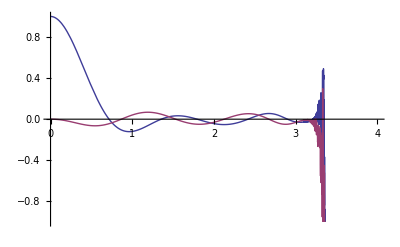

```mathematica
Ge={Re[#],Im[#]}&[Un[En,2,250,x][[1]]];Plot[Ge,{x,0,4},PlotRange->{-1,1}]
```